## 1：集合的交

```mathematica
A=Reduce[0 < x < 2, x];
B=Reduce[x≥1,x];
B1=Complement[B];
```

```mathematica
Intersection[A,B1]
```

Intersection::heads: 位置 2 和 1 处的头部 GreaterEqual 和 Inequality 应该是一样的.

(0<x<2)∩(1≥x)

## 2:线性规划

```mathematica
Maximize[{3x+5y,x+y≤5,2x-y≤4,-x+y≤1,y≥0},{x,y}]
```

{21,{x→2,y→3}}

## 3:算法

```mathematica
n:=20;
T:=0;
For[i=2,i<5,i++,If[Mod[n,i]==0,T=T+1]]
```

```mathematica
T
```

2

## 5：排序

```mathematica
Clear[a,b,c]
```

```mathematica
x1:={Log2[E],a};(*这样做最后排序以后带上各自的顺序*)
x2:={Log[2],b};
x3:={Log[1/2,1/3],c};
Sort[{x1,x2,x3},#1[[1]]>#2[[1]]&](*按照第一个排序*)
```

{{Log[3]/Log[2],c},{1/Log[2],a},{Log[2],b}}

## 6：画图并确定单调区间

```mathematica
Clear[a,t];
(*需要输入的一些参数：*)
a:=2;(*和周期有关的系数*)
period=2*Pi/a;
```

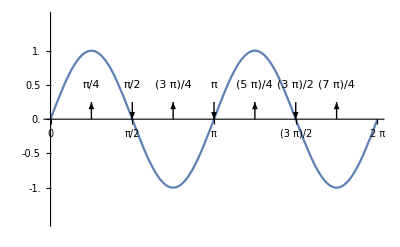

```mathematica
f[t_]:=Sin[a(t-Pi/10)+Pi/5];
sol1=t/.Solve[{f[t]==0,0<t<2*Pi},t];(*与坐标轴的交点*)
sol2=t/.Solve[{D[f[t],t]==0,0<t<2*Pi},t];(*顶点*)
Plot[f[t],{t,0,2*Pi},Ticks->{Range[0,2*Pi,period/4],Range[-1,1,0.5]},PlotRange->{{0,2*Pi},{-1.5,1.5}},Epilog->{Arrow[{{#,0.25},{#,0}}]&/@sol1,Text[#,{#,1/2}]&/@sol1,Arrow[{{#,0},{#,0.25}}]&/@sol2,Text[#,{#,1/2}]&/@sol2}] 
(*1：这里面Arrow是绘制箭头，需要输入的参数是箭头起始和终止的坐标。本例中用#替换最后加入&定义一个pure function*)
(*后面#被替代的部分指向sol,\表示替换，@sol是调用前面定义的sol*)
(*2:Ticks代表画图的刻度，第一个参数里面的表示x轴上的刻度，第二个参数表示y轴上的刻度*)
(*Range是取范围，搭配Ticks于Range使用可以按照指定的起始和终点，指定的间距标记刻度*)
```

## 7：求双曲线的参数

```mathematica
Clear[a,b,c,d1,d2,e,sol];
```

```mathematica
(*条件1：离心率*)
e:=2;
(*条件2：交点到渐近线的距离*)
sol={x,y}/. Solve[{x^2/a^2-y^2/b^2==1,x==Sqrt[a^2+b^2]},{x,y}];
```

```mathematica
(*定义点到直线距离函数： *)
distance2Line[x_,y_,a_,b_,c_]:=Abs[a*x+b*y+c]/Sqrt[a^2+b^2];
```

```mathematica
(*计算两个交点到直线距离*)
```

```mathematica
d1=distance2Line[sol[[1]][[1]],sol[[1]][[2]],1/a,-1/b,-1];
d2=distance2Line[sol[[2]][[1]],sol[[2]][[2]],1/a,-1/b,-1];
```

```mathematica
Solve[{d1+d2==6,Sqrt[a^2+b^2]/a==2},{a,b}] (*综合两个条件解方程*)
```

{{a→2,b→-2 √3},{a→2,b→2 √3}}

## 9:复数的运算

```mathematica
(6+7I)/(1+2I)
```

4-ⅈ

## 10:多项式展开

```mathematica
Expand[(x-1/(2*Sqrt[x]))^5]
```

-1/(32 x^(5/2))+5/(16 x)-(5 √x)/4+(5 x^2)/2-(5 x^(7/2))/2+x^5

## 18:数列相关问题

```mathematica
Clear[a,b,q,k1,k2,T];
```

```mathematica
(*先定义等比，等差数列*)
a[n_]:=q^(n-1);
b[n_]:=k1*n+k2;
```

```mathematica
(*计算参数*)
list={k1,k2,q}/.Solve[{a[3]==a[2]+2,a[4]==b[3]+b[5],a[5]==b[4]+2*b[6],q>0},{k1,k2,q}];
k1=list[[1]][[1]];
k2=list[[1]][[2]];
q=list[[1]][[3]];
```

```mathematica
(*求Tn*)
```

```mathematica
Sum[a[k], {k, 1, n}]
```

-1+2^n

```mathematica
S[n_]:=2^n-1;
Sum[S[k],{k,1,n}];
```

```mathematica
T[n_]:=-2+2^(1+n)-n;
```

```mathematica
(*最后的和*)
Sum[((T[k]+b[k+2])*b[k])/((k+1)*(k+2)),{k,1,n}]
```

(2 (-2+2^(1+n)-n))/(2+n)

## 19：Question about ellipse

```mathematica
Clear[a,b,c,FB,AB,sol,k,sol1,sol2];
```

```mathematica
(*Find the standard equation of the ellipse*)
```

```mathematica
(*Eulidean distance between two points on the plane *)
c=Sqrt[a^2-b^2];
FB=EuclideanDistance[{-c,0},{0,b}];
AB=EuclideanDistance[{b,0},{0,b}];
```

```mathematica
sol={a, b} /. Solve[{c/a == Sqrt[5]/3, FB*AB == 6 Sqrt[2], a > b > 0}, {a, b}];
a=sol[[1]][[1]];
b=sol[[1]][[2]];
```

```mathematica
(*Calculating intersection point P*)
sol1={x,y}/.Solve[{y==k*x,x^2/a^2+y^2/b^2==1,k>0,x>0,y>0},{x,y}];
(*Calculating the intersection point of two lines Q*)
(*Calcualting the equation of the line through theses two points*)
line[p1_,p2_,x_]:=((p1[[2]]-p2[[2]])/(p1[[1]]-p2[[1]]))*(x-p1[[1]])+p1[[2]];
sol2={x,y}/.Solve[{y==k*x,y==line[{b,0},{0,b},x],k>0},{x,y}];
```

```mathematica
(*Distances*)
AQ=EuclideanDistance[{b,0},sol2[[1]]];
PQ=EuclideanDistance[sol1[[1]],sol2[[1]]];
OQ=EuclideanDistance[{0,0},sol2[[1]]];
OA=EuclideanDistance[{0,0},{b,0}];
(*Angles*)
vectorOQ=sol2[[1]];
vectorOA={b,0};
sinAngel=Sqrt[1-(vectorOQ.vectorOA/(OA*OQ))^2];(*Do not use the VectorAngle function here,otherwise the result will be very complicated,calculate the Sin instead of the Angle !*)
```

```mathematica
(*Get the k*)
Solve[AQ/PQ==(5Sqrt[2]/4)*sinAngel,k]
```

{{k→11/28},{k→1/2}}

## 20：含参数的函数问题

```mathematica
Clear[h,g,f,x1,x2,k1,k2];
```

```mathematica
(*单调区间问题*)
h[x_]:=a^x-x*Log[a];
g[x_]:=Log[a,x];
f[x_]:=a^x;
Reduce[D[h[x],x]>0&&a>1,{x},Reals]
```

a>1&&x>0

```mathematica
(*切线问题*)
(*切线平行建立方程*)
k1:=D[f[x],x]/.x->x1;
k2:=D[g[x],x]/.x->x2
Reduce[{k1==k2},{x1},Reals]
```

Log[a]≠0&&(0<a<1||a>1)&&x2>0&&x1==Log[1/(x2 Log[a]^2)]/Log[a]

```mathematica
x1=Log[1/(x2 Log[a]^2)]/Log[a];
(*由于Simplify,FullSimplify都不能对x1+g[x2]进行化简,因此需要自定义化简规则*)
(*自定义化简规则*)
collectLog[expr_]:=Module[{rule1,rule2,rule3,a,b},rule1=Log[a_]+Log[b_]->Log[a*b];
rule2=Log[(a_)^(b_)]->(b)*Log[a];
(expr/.rule1)/.rule2];
(*应用上述化简规则*)
expr=x1+g[x2];
expr2=Simplify[expr,TransformationFunctions->{Automatic,ComplexExpand}]//collectLog (*加//可以实现函数的嵌套，不用一直加括号*)
```

-(2 Log[Log[a]])/Log[a]

```mathematica
(*切线问题证明解的存在性*)
Clear[x1,y1,x2,y2,k];
(*当a=e^(1/e)*)
l[x_]:=k*x+b;
sol4=x/.Solve[f[x]==l[x],x];
x1:=sol4[[1]];

sol5=x/.Solve[f[x]==l[x],x];
x2:=sol5[[1]];
k3=D[f[x],x]/.x->x1;
k4=D[f[x],x]/.x->x2;
k=(y1-y2)/(x1-x2);
```

```mathematica
Solve[{y1==f[x1],y2==g[x2],k3==k,k4==k},{k}]
```

{{k→1/Log[b+1/Log[a]]}}